```mathematica
Clear[flipbook]
flipbook={};
For[n=0,n≤1000,n++,
data=Import["//Users/diegolallemand/phys/med/project/output/all/grain"<>ToString[n]<>".txt","Table"];
list={};
For[i=1,i≤Length[data],i++,
x=data[[i]][[2]];
y=data[[i]][[3]];
a=data[[i]][[6]];
r=data[[i]][[7]];

list=Join[list,{{Gray,Disk[{x,y},r]},{Black,Arrowheads[0.01],Arrow[{{x,y},{x,y}+r*{Cos[a],Sin[a]}}]}}];
];
flipbook = Join[flipbook,{Graphics[list]}];
]; 
ListAnimate[flipbook]
```

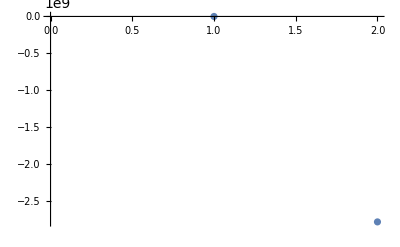

```mathematica
data={};
indices={4,6,8,12,16};
For[i=1,i<=Length[indices],i++,n=indices[[i]];
tmp=Import["//Users/diegolallemand/phys/med/project/output/ft_"<>ToString[n]<>".txt","Table"];
data=Join[data,tmp]]
ListPlot[data[[2]]]
```

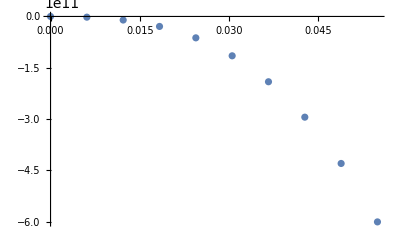

```mathematica
data = Import["//Users/diegolallemand/phys/med/project/output/ft_4.txt","Table"];
ListPlot[data]
```